# Notebook for computing the spectrum of linearized KdV-Mathieu Operator

This notebook computes the spectrum of the eigenvalue problem 
 
This is in the form of a linearized gKdV type operator, but does not come from the linearization around a gKdV traveling wave profile.

```mathematica
A0 = 4;
A1 = 5;
Period = 2 Pi;
Pot[x_] := (4 + 5 Cos[x]);
```

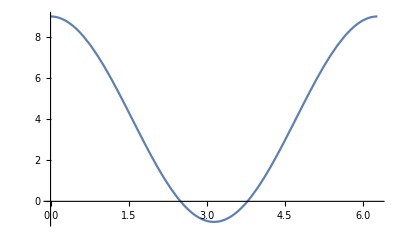

```mathematica
Plot[Pot[x],{x,0,Period}]
```

The code snippet below solves the ODE defining the linearized operator as well as the derivative of this ODE with respect to the eigenvalue parameter λ. This will allow us to generate the monodromy matrix as well as the derivative of the monodromy matrix with respect to the eigenvalue parameter λ. The derivatives are necessary for computing the bifurcation index. 

Note that we are actually solving the adjoint equation here, rather than the forward equation. The two are isospectral, so we can do either.

```mathematica
SolMonodromy[l_] := NDSolve[{r1'''[x] + (Pot[x]) r1'[x] - l r1[x]==0,dr1'''[x] + (Pot[x]) dr1'[x] - l dr1[x]-r1[x]==0,r2'''[x] + (Pot[x] ) r2'[x] - l r2[x]==0,dr2'''[x] + (Pot[x] ) dr2'[x] - l dr2[x]- r2[x]==0,r3'''[x] + (Pot[x]) r3'[x] - l r3[x]==0 ,dr3'''[x] + (Pot[x]) dr3'[x] - l dr3[x]-r3[x]==0 ,r1[0]==1,r1'[0]==0,r1''[0]==0,r2[0]==0,r2'[0]==1,r2''[0]==0,r3[0]==0,r3'[0]==0,r3''[0]==1,dr1[0]==0,dr1'[0]==0,dr1''[0]==0,dr2[0]==0,dr2'[0]==0,dr2''[0]==0,dr3[0]==0,dr3'[0]==0,dr3''[0]==0},{r1,r2,r3,dr1,dr2,dr3},{x,0,Period}];
mono[l_] := Evaluate[{{r1[Period],r2[Period],r3[Period]},{r1'[Period],r2'[Period],r3'[Period]},{r1''[Period],r2''[Period],r3''[Period]}}] /. SolMonodromy[l][[1]]
```

The monodromy should have a single eigenvalue of 1 at λ=0, since the constant function is in the kernel of the adjoint operator.  Since this does not arise as the stability problem for a multi-parameter family of traveling waves we do not expect a triple eigenvalue of one for μ=0. We can see that there is a single eigenvalue of 1, and that the other two eigenvalues lie on the unit circle as well.

```mathematica
MatrixForm[mono[0]]
```

(1. | 7.79175 | -0.621149
0. | -0.31511 | -0.0545988
0. | 16.4968 | -0.315108)

```mathematica
Eigenvalues[mono[0]]
```

{1.+0. ⅈ,-0.315109+0.949055 ⅈ,-0.315109-0.949055 ⅈ}

The code snippets below compute the characteristic polynomial of the monodromy matrix (CharPoly[λ]), the complex Floquet discriminant (FloqD), the derivative with respect to λ of the  Floquet discriminant (FloqDp), the discriminant of the characteristic polynomial (Disco) and the bifurcation index (BifIndex)

```mathematica
CharPoly[l_] := CharacteristicPolynomial[mono[l] , μ ];
MonoRoots[l_] := μ /. Solve[CharPoly[l]==0,μ];
FloqD[l_] := (Evaluate[r1[Period] + r2'[Period] + r3''[Period]]/. SolMonodromy[l])[[1]]
FloqDp[l_] := (Evaluate[dr1[Period] + dr2'[Period] + dr3''[Period]]/. SolMonodromy[l])[[1]]
Disco[λ_] := Evaluate[(-27-4 Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^3+18 Conjugate[r1[Period]+r2'[Period]+r3''[Period]] (r1[Period]+r2'[Period]+r3''[Period])+Conjugate[r1[Period]+r2'[Period]+r3''[Period]]^2 (r1[Period]+r2'[Period]+r3''[Period])^2-4 (r1[Period]+r2'[Period]+r3''[Period])^3)]/. SolMonodromy[λ][[1]]
BifIndex[l_] := Module[{FF = FloqD[l],FP=FloqDp[l],FPC = Conjugate[FP]},FP^3 + Conjugate[FP]^3 + FF FP Conjugate[FP]^2 + Conjugate[FF] Conjugate[FP] FP^2 ]
```

The plot below depicts the bifurcation index along the imaginary axis (by symmetry this is a real quantity for λ purely imaginary. The plot is turned 90° so that we can see where the plot crosses the y-axis. Those crossings mark bifurcation points.

```mathematica
BifIndexPlot=ParametricPlot[{BifIndex[I l],l},{l,-10,19},PlotRange->{{-3,3},{-10,10}},PlotStyle->{Red,Thick,Dashed}]
```

-Graphics-

```mathematica
Discrim[l_] := Re[Discriminant[CharPoly[l],μ]]
```

```mathematica
Mult[λ_] := If[Discrim[λ]<0,.02,.005I]
```

```mathematica
Discrim[0.2I]
```

-26.5834

```mathematica
Mult[0.5I]
```

0.+0.005 ⅈ

```mathematica
Mult[4.0I]
```

0.+0.005 ⅈ

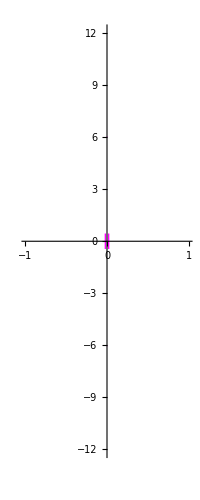

```mathematica
MultiplicityGraph1=ParametricPlot[{Mult[I z],z},{z,-12,12},PlotStyle->{Thick,Magenta},PlotRange->{{-1,1},{-12,12}}];
MultiplicityGraph2=ParametricPlot[{-Mult[I z],z},{z,-12,12},PlotStyle->{Thick,Magenta}];
MultiplicityGraph3=ParametricPlot[{-.1*Mult[I z],z},{z,6,6.2},PlotStyle->{Thick,Magenta}];
MultiplicityGraph4=ParametricPlot[{.1*Mult[I z],z},{z,6,6.2},PlotStyle->{Thick,Magenta}];
MultiplicityGraph5=ParametricPlot[{.1*Mult[I z],z},{z,-6.2,-6},PlotStyle->{Thick,Magenta}];
MultiplicityGraph6=ParametricPlot[{-.1*Mult[I z],z},{z,-6.2,-6},PlotStyle->{Thick,Magenta}];
Show[MultiplicityGraph1,MultiplicityGraph2,MultiplicityGraph3,MultiplicityGraph4,MultiplicityGraph5,MultiplicityGraph6]
```

The graph above shows the spectral multiplicity along the imaginary axis. The multiplicity is either one or three on open sets. The magenta intervals denote regions of multiplicity three. There is one interval near the origin and two very small intervals at around ±6 i , ±6.05i .

The graph below depicts the  deltoid curve.  Along the imaginary axis the spectral multiplicity is three if and only if the Floquet discriminant lies inside the deltoid.

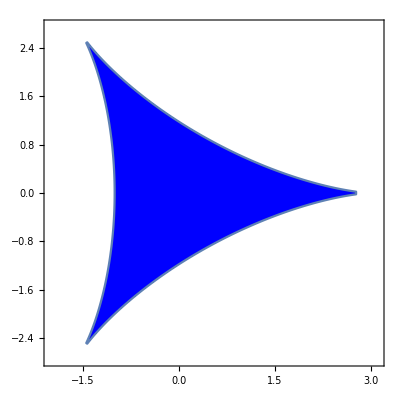

```mathematica
Deltoid1=RegionPlot[-27+18 a^2-8 a^3+a^4+18 b^2+24 a b^2+2 a^2 b^2+b^4<0,{a,-3,3.5},{b,-3.25,3.25},PlotPoints->100,PlotRange->{{-2,3.1},{-2.75,2.75}},PlotStyle->Blue]
```

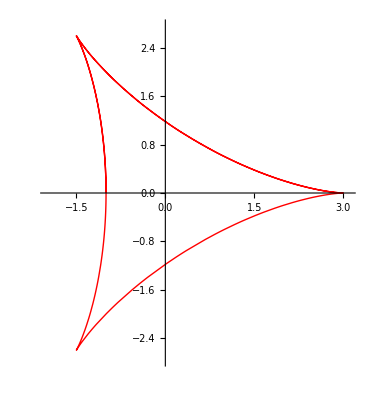

```mathematica
(* This is the Cartesian *)
Astroid[a_,b_,r_] := ParametricPlot[ -r{(a-b) Cos[t] + b Cos[(a-b)/b t],(a-b) Sin[t] + b Sin[(a-b)/b t]},{t,0,6Pi},PlotStyle->{Thick,Red},PlotRange->{{-2,3.1},{-2.75,2.75}}]  
Deltoid2=Astroid[1,2,1]
```

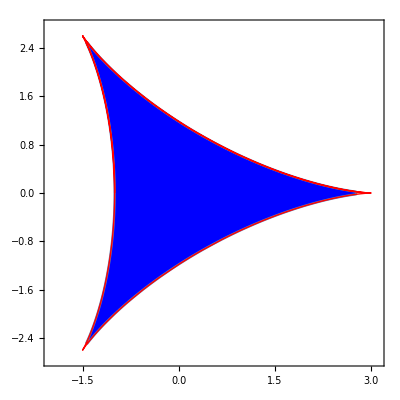

```mathematica
Deltoid3=Show[Deltoid1,Deltoid2]
```

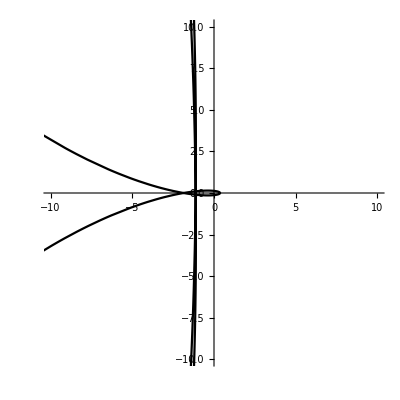

```mathematica
FDPlot=ParametricPlot[{Re[FloqD[I λ]],Im[FloqD[I λ]]},{λ,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->Black]
```

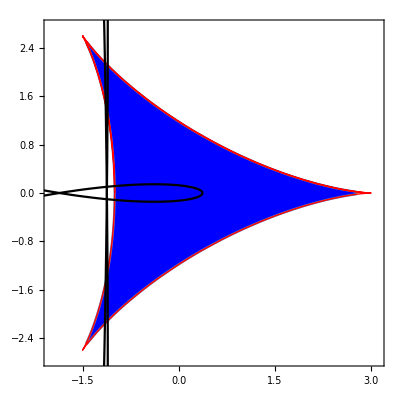

```mathematica
Delt2=Show[Deltoid3,FDPlot]
```

```mathematica
L = Period;
NM = 25;
dx = L/NM;diag = Table[2*Pi*I*1.0(NM-j)/Period,{j,1,2*NM+1}];D1=DiagonalMatrix[diag];
FM = Table[0,{i,1,4*NM+1}];
FM[[2*NM+1]]=A0;
FM[[2*NM]]=A1/2;
FM[[2*NM+2]]=A1/2;
FCol = Table[FM[[2NM+2-i]],{i,1,2*NM+1}];
FRow = Table[FM[[i]],{i,2*NM+1,4*NM+1}];
Pot2[x_] := Re[Sum[FM[[k]] Exp[2 Pi I (k-(2*NM+1)) x/Period],{k,1,4*NM+1}]];
PotM = ToeplitzMatrix[Re[FCol],Re[FRow]];
D3=D1.D1.D1;D2=D1.D1;D0=IdentityMatrix[2NM+1];
```

Eig[q] and Eig2[q] compute the spectrum with quasi-periodic boundary conditions v(L) = exp(2 π i q/L) v(0). Eig computes the spectrum of the linearized operator and Eig2 computes the spectrum of the adjoint. These should be isospectral.

```mathematica
Eig[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 +  PotM.(D1 - I q D0)];
Eig2[q_] := Eigenvalues[D3 - 3I q D2 -3q^2 D1 + I q^3 D0 + (D1 - I q D0). PotM];
```

```mathematica
Chop[Eig[0.0]]
Chop[Eig2[0.0]]
```

{0.+17474.1 ⅈ,0.+15525. ⅈ,0.-13730.1 ⅈ,0.+13728. ⅈ,0.-12075. ⅈ,0.+12075. ⅈ,0.-10560. ⅈ,0.+10560. ⅈ,0.-9177. ⅈ,0.+9177. ⅈ,0.-7920. ⅈ,0.+7920. ⅈ,0.-6783. ⅈ,0.+6783. ⅈ,0.+5760. ⅈ,0.-5760. ⅈ,0.+4845. ⅈ,0.-4845. ⅈ,0.+4032. ⅈ,0.-4032. ⅈ,0.+3315. ⅈ,0.-3315. ⅈ,0.+2688. ⅈ,0.-2688. ⅈ,0.+2145. ⅈ,0.-2145. ⅈ,0.-1680. ⅈ,0.+1680. ⅈ,0.-1287. ⅈ,0.+1287. ⅈ,0.+960.004 ⅈ,0.-960.004 ⅈ,0.-693.006 ⅈ,0.+693.006 ⅈ,0.-480.008 ⅈ,0.+480.008 ⅈ,0.-315.013 ⅈ,0.+315.013 ⅈ,0.-192.021 ⅈ,0.+192.021 ⅈ,0.-105.037 ⅈ,0.+105.037 ⅈ,0.+48.075 ⅈ,0.-48.075 ⅈ,0.-15.1958 ⅈ,0.+15.1958 ⅈ,0.-6.03305 ⅈ,0.+6.03305 ⅈ,0.-0.571534 ⅈ,0.+0.571534 ⅈ,0}

{0.+17474.1 ⅈ,0.+15525. ⅈ,0.-13730.1 ⅈ,0.+13728. ⅈ,0.-12075. ⅈ,0.+12075. ⅈ,0.-10560. ⅈ,0.+10560. ⅈ,0.-9177. ⅈ,0.+9177. ⅈ,0.+7920. ⅈ,0.-7920. ⅈ,0.-6783. ⅈ,0.+6783. ⅈ,0.+5760. ⅈ,0.-5760. ⅈ,0.+4845. ⅈ,0.-4845. ⅈ,0.+4032. ⅈ,0.-4032. ⅈ,0.+3315. ⅈ,0.-3315. ⅈ,0.+2688. ⅈ,0.-2688. ⅈ,0.+2145. ⅈ,0.-2145. ⅈ,0.+1680. ⅈ,0.-1680. ⅈ,0.+1287. ⅈ,0.-1287. ⅈ,0.-960.004 ⅈ,0.+960.004 ⅈ,0.+693.006 ⅈ,0.-693.006 ⅈ,0.-480.008 ⅈ,0.+480.008 ⅈ,0.-315.013 ⅈ,0.+315.013 ⅈ,0.+192.021 ⅈ,0.-192.021 ⅈ,0.-105.037 ⅈ,0.+105.037 ⅈ,0.-48.075 ⅈ,0.+48.075 ⅈ,0.+15.1958 ⅈ,0.-15.1958 ⅈ,0.-6.03305 ⅈ,0.+6.03305 ⅈ,0.+0.571534 ⅈ,0.-0.571534 ⅈ,0}

This is somewhat lower resolution than the figure in the paper, in the interest of reducing the file size. In the figure from the paper the step size for Q was .0001. This can be easily modified by replacing the .001 in the Do loop  {Q,-1,1,.0025} to whatever the desired Floquet multiplier spacing is.

```mathematica
frame=Plot[0,{x,-0.5,0.5},PlotRange->{{-1,1},{-.5,.5}}];
l = {}
Do[l=Join[l,Eig[Q]],{Q,-1,1,.001}]
Dimensions[l]
```

{}

{102051}

```mathematica
Dimensions[l]
```

{102051}

Find the largest real part to set the scale appropriately.

```mathematica
Max[Re[l]]
```

0.460805

The plot below shows a pair of isolas near the origin, together with a band of multiplicity three spectrum.

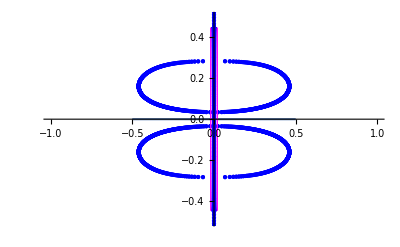

```mathematica
Figure3A= Show[frame,ComplexListPlot[l,PlotStyle->{Blue,PointSize[Small]}],BifIndexPlot,MultiplicityGraph1,MultiplicityGraph2,MultiplicityGraph3,MultiplicityGraph4,MultiplicityGraph5,MultiplicityGraph6]
```

```mathematica
frame2=Plot[0,{x,-0.5,0.5},PlotRange->{{-.1,.1},{5.95,6.15}}];
```

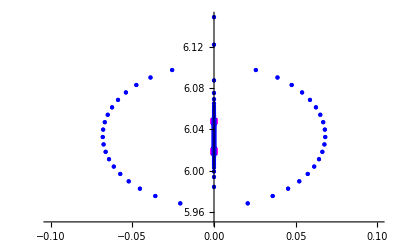

```mathematica
Figure3B= Show[frame2,ComplexListPlot[l,PlotStyle->{Blue,PointSize[Small]}],BifIndexPlot,MultiplicityGraph1,MultiplicityGraph2,MultiplicityGraph3,MultiplicityGraph4,MultiplicityGraph5,MultiplicityGraph6]
```